```mathematica
f[y_] := 1.2 - 0.3*y^2
```

```mathematica
Zf[y_] := 25 + 3*Sin[17.951958020513104 * y]
```

```mathematica
R= 0.7
n2 = 1
ω = 3.1 * 10^14 
α = -25 Degree
y0 = -0.1
```

```mathematica
n1[y_] := f[y]*(1-((0.35*10^14)/ω)^2)
```

```mathematica
curH = y0
step = 0.001
distance = 0
rayLen=0
dots = List[]
direction = -1
sinGamma = Sin[Pi/2 - ArcSin[Sin[α]/n1[curH]]]
nGamma = n1[curH]
```

```mathematica
While[distance <= Zf[curH],
curH += step * Sqrt[1 - sinGamma^2] * direction;
If[Abs[curH] >= R, nBeta = n2, nBeta = n1[curH]];
sinBeta = (nGamma * sinGamma)/nBeta;
If[sinBeta > 1, sinBeta = sinGamma; direction *= -1];
rayLen += step;
distance += sinBeta * step;
sinGamma = sinBeta;
nGamma = nBeta;
AppendTo[dots, {distance, curH}];
];
Print[rayLen];
```

25.148

{}

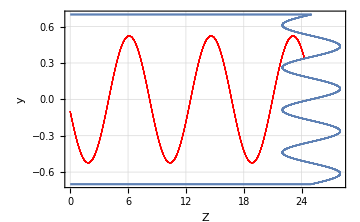

```mathematica
rightSide = {}
For[i = -R, i < R, i+= 0.0001, AppendTo[rightSide, {Zf[i], i}]]

Show[
ListPlot[dots,PlotStyle->{PointSize[0.002], Red}, PlotRange->All,Frame->True,GridLines->Automatic, AxesLabel -> {"Z", "y"}],
ListPlot[rightSide,PlotRange->All, Frame-> True],
 Plot[0.7,{x,0,25},PlotRange->{0,1}], 
Plot[-0.7,{x,0,25},PlotRange->{-1,0}],
PlotRange->All,AxesLabel->{"Z","y"}]
```